## PHAS0012 Computing for Mathematical Physics 2019/20

# Homework 8

# Mark for homework 8: /70 (to be competed by your marker)

# Feedback from marker: (to be competed by your marker)

# Which feedback from your last homework are you employing in this homework? Marks will be deducted if you do not complete this section. Implemented text and subsections; now also used code cells format to make clearer, and have broken up code cells for better readability- this is from week 1 and 3 feedback, had no feedback on week 2. From week 5 I have ensured to label all graphs

# Give your answers in the code cells labelled “(*your solution here*)”

## Question1

#### Part a:

1. (a) Obtain a numerical solution of 
                d^2 y/d t^2  + y^3= 7 cos(5 t)
with boundary conditions y(-1) = y(10) = 0, over the range -1 <t <10. Explore the NDSolve options in order to find a solution that has an accuracy of 4 digits and a precision of 6 digits. Plot your result over the same range of t. [10 marks for 1a]

```mathematica
exp1a= y''[t]+y[t]^3==7 Cos[5 t]
exp1b= {y[-1]==0, y[10]==0}
sol1=NDSolve[{exp1a,exp1b},y,{t,-1,10},AccuracyGoal->4, PrecisionGoal->6]
```

y[t]^3+y''[t]==7 Cos[5 t]

{y[-1]==0,y[10]==0}

{{y→InterpolatingFunction[…]}}

InterpolatingFunction[…][t]

(InterpolatingFunction[…][t])^3+InterpolatingFunction[…][t]==7 Cos[5 t]

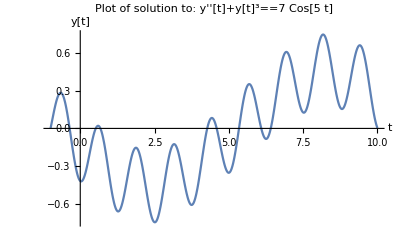

```mathematica
yt= y[t]/.sol1[[1]]
exp1c= D[yt,{t,2}]+yt^3==7Cos[5 t]
Plot[yt,{t,-1,10},AxesLabel->{"t","y[t]"},
PlotLabel-> "Plot of solution to: y''[t]+y[t]^3==7 Cos[5 t]" ]
```

#### Part b:

(b) NDSolve as used in part (a) finds one of many possible solutions to the equation. Adapt the shooting method described in the lecture to explore some of the other solutions. Proceed by writing an appropriate function and using a suitable plot to examine the values of y(10) as a function of y'(-1) when solving with the boundary value y(-1)=0 - do this for y'(-1) values between -5 and 5.  Use FindRoot to find and compare the solutions given by the two solutions lying between y'[-1]=0 and y'[-1]=1 - a plot of the two solutions is a useful way to compare. [20 marks for 1b]

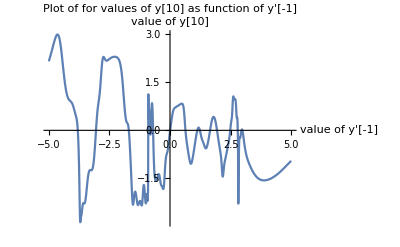

```mathematica
f1a[x_]:=NDSolve[{exp1a, y[-1]==0, y'[-1]==x},y[t],{t,-1,10}]
f2a[x_?NumericQ]:=((y[t]/.f1a[x][[1]])/.t->10.)
Plot[f2a[x],{x,-5,5},
AxesLabel->{" value of y'[-1]", "value of  y[10]"},
PlotLabel-> "Plot of for values of y[10] as function of y'[-1]"]
```

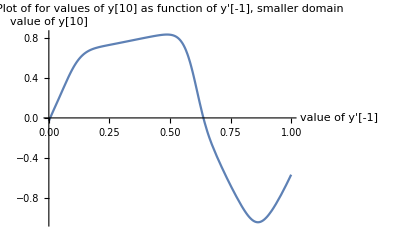

{x→0.00550158}

{x→0.63786}

```mathematica
Plot[f2a[x],{x,0,1},AxesLabel->{" value of y'[-1]", "value of  y[10]"},
PlotLabel-> "Plot of for values of y[10] as function of y'[-1], smaller domain"]
ssol1a=FindRoot[f2a[x]==0,{x,0,0.2}]
ssol1b=FindRoot[f2a[x]==0,{x,0.6,0.8}]
```

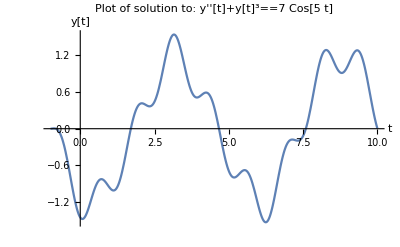

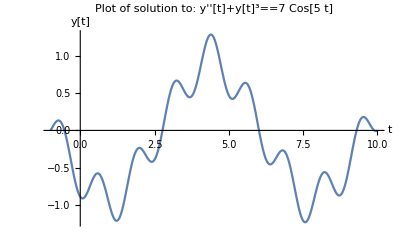

```mathematica
Plot[Evaluate[y[t]/.f1a[x/.ssol1a][[1]]],{t,-1,10},AxesLabel->{"t","y[t]"},
PlotLabel-> "Plot of solution to: y''[t]+y[t]^3==7 Cos[5 t]" ]
Plot[Evaluate[y[t]/.f1a[x/.ssol1b][[1]]],{t,-1,10},AxesLabel->{"t","y[t]"},
PlotLabel-> "Plot of solution to: y''[t]+y[t]^3==7 Cos[5 t]" ]
```

InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

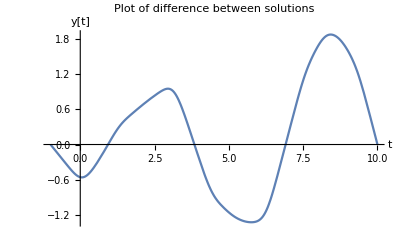

```mathematica
dy1[t_]=y[t]/.f1a[x/.ssol1a][[1]]
dy2[t_]=y[t]/.f1a[x/.ssol1b][[1]]
Plot[dy1[t]-dy2[t],{t,-1,10},AxesLabel->{"t","y[t]"},
PlotLabel-> "Plot of difference between solutions" ]
```

As we can see the solutions are fairly similar visually however, moved out of phase as shown by the plot of the difference which is near sinusoidal. It is not just out of phase there is some difference in the modulation of the wave.

## Question2:

2. Two particles, each of unit mass in some system of units, move along the x axis and are joined by a spring of natural length 1 and spring constant 5.  They particles are initially released from rest with one particle at x=0.1 and the other at x=0.9 Set up and solve numerically the equations for their subsequent motion up to time 100, and plot your results.

#### Part a: Solving differential equation

```mathematica
exp2a= m1*x1''[t]==-k(x0-Abs[x2[t]-x1[t]])
exp2b= m2*x2''[t]== k(x0-Abs[x2[t]-x1[t]])
```

m1 x1''[t]==-k (x0-Abs[-x1[t]+x2[t]])

m2 x2''[t]==k (x0-Abs[-x1[t]+x2[t]])

We have two differential equations set up, the equations show SHM as the particle experience force due to the springs compression and rarefaction, the forces are equal and opposite as no other external forces.

```mathematica
vals={m1->1,m2->1,k->5,x0->1};
exp2c=exp2a/.vals
exp2d=exp2b/.vals
```

x1''[t]==-5 (1-Abs[-x1[t]+x2[t]])

x2''[t]==5 (1-Abs[-x1[t]+x2[t]])

```mathematica
sol2a=NDSolve[{exp2c,exp2d, x1[0]==0.1, x2[0]==0.9, x1'[0]==0, x2'[0]==0},{x1[t],x2[t]},{t,0,100}]
```

{{x1[t]→InterpolatingFunction[…][t],x2[t]→InterpolatingFunction[…][t]}}

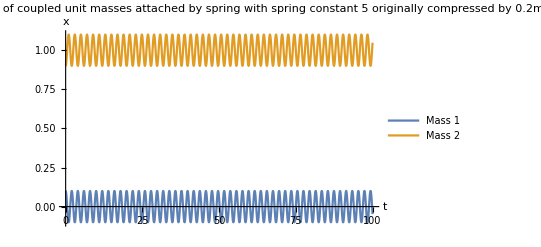

```mathematica
Plot[{Evaluate[x1[t]/.sol2a[[1,1]]],Evaluate[x2[t]/.sol2a[[1,2]]]},{t,0,100},
PlotLegends->{"Mass 1","Mass 2"},AxesLabel->{"t","x"},
PlotLabel-> "Plot of the motions of coupled unit masses 
attached by spring with spring
 constant 5 originally compressed by 0.2m"]
```

#### Part B: Graph for Total Mechanical Energy

Also calculate the total energy and plot it as a function of time (the kinetic energy of a particle of mass m moving with velocity v is m v^2/2 and the elastic energy in a spring of natural length L and spring constant k when its length is d is (k(L-d))^2/2: at that point the force in the spring is k(L-d).

```mathematica
KE[x_]:=1/2(D[x/.sol2a,t])^2
EL[x1_,x2_]:=5/2(1-(x2-x1))^2/.sol2a
```

Setting up functions to calculate kinetic and elastic potential energy

```mathematica
Ke1=KE[x1[t]];
Ke2 =KE[x2[t]];
Ele =EL[x1[t],x2[t]];
Etot = Ke1-Ke2+Ele //Simplify
```

{1/2 (5 (1+InterpolatingFunction[…][t]-InterpolatingFunction[…][t])^2+(InterpolatingFunction[…][t])^2-(InterpolatingFunction[…][t])^2)}

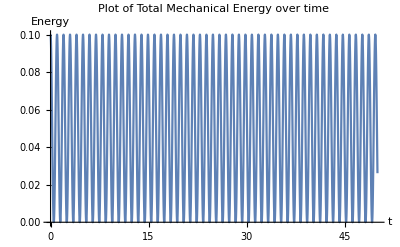

```mathematica
Plot[Etot, {t,0,50},
AxesLabel->{"t","Energy"},
PlotLabel-> "Plot of Total Mechanical Energy over time"]
```

#### Part c: Greater compression:

Repeat for the case in which the particles are released from rest at x=0.3 and x=0.5, and again plot the two graphs, choosing the range displayed so as to show any trends, and comment on your results. [20 marks]

```mathematica
sol2b=NDSolve[{exp2c,exp2d, x1[0]==0.3, x2[0]==0.5, x1'[0]==0, x2'[0]==0},{x1[t],x2[t]},{t,0,100}]
```

{{x1[t]→InterpolatingFunction[…][t],x2[t]→InterpolatingFunction[…][t]}}

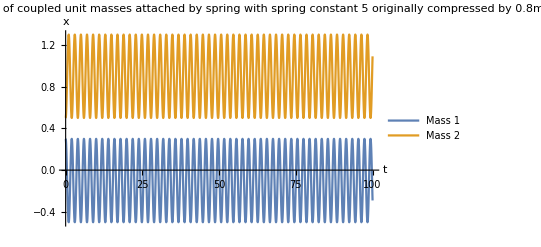

```mathematica
Plot[{Evaluate[x1[t]/.sol2b[[1,1]]],Evaluate[x2[t]/.sol2b[[1,2]]]},{t,0,100},
PlotLegends->{"Mass 1","Mass 2"},AxesLabel->{"t","x"},
PlotLabel-> "Plot of the motions of coupled unit masses 
attached by spring with spring
 constant 5 originally compressed by 0.8m"]
```

Here we see with much greater compression the oscillations are much greater as there is more stored elastic energy in the begin

## Question 3:

3. This is a question from a past paper. 
The following equations describe, in simplified form,  a set of chemical reactions involving bromous ions, bromide ions and cerium in two different oxidation states:
ϵ dx/dt= q y - x y + x(1-x), 
δ dy/dt= -q y - x y +2 f z,
 dz/dt=   x - z.
 The variables x, y and z are functions of time t, and represent the concentrations of HBrO_2, Br^- and Ce^(4+)respectively, and ϵ, q, δ and f are constants.
 (a) Write the equations in Mathematica form, and solve the list  of differential equations numerically, over the range 0≤t≤40, with the initial conditions x=y=z=1 and the parameters ϵ = 5 x 10^-5, δ = 2 x 10^-4, q = 8 x 10^-4, and f = 0.5. Plot  your solutions for x,y and z over the same range of t.  [3+2+3]

#### Set up equations:

```mathematica
deq3a =x'[t] ==1/ϵ( q y[t] -x[t] y[t] +x[t] (1-x[t]))
deq3b= y'[t]== 1/δ(-q y[t] -x[t] y[t] +2 f z[t])
deq3c = z'[t] == x[t]-z[t]
```

x'[t]==((1-x[t]) x[t]+q y[t]-x[t] y[t])/ϵ

y'[t]==(-q y[t]-x[t] y[t]+2 f z[t])/δ

z'[t]==x[t]-z[t]

#### Part a :

```mathematica
val3a = {ϵ-> 5 10^(-5),δ->  2 10^(-4), q -> 8 10^(-4),f-> 0.5}
sol3a = NDSolve[{{deq3a, deq3b, deq3c} /. val3a, x[0] == y[0] == z[0] == 1}, {x[t], y[t], z[t]}, {t, 0, 40}]
```

{ϵ→1/20000,δ→1/5000,q→1/1250,f→0.5}

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],z[t]→InterpolatingFunction[…][t]}}

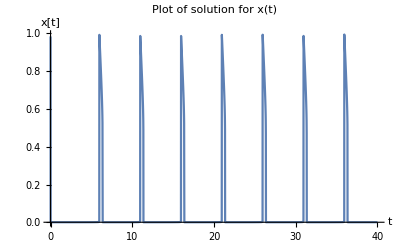

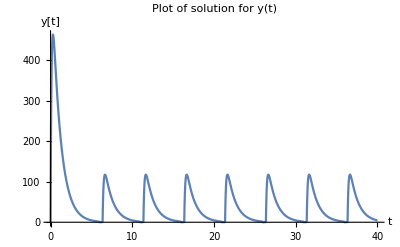

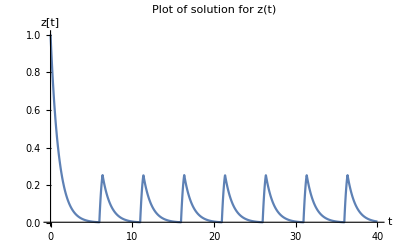

```mathematica
Plot[x[t] /. sol3a, {t, 0, 40}, PlotRange->Full, AxesLabel->{"t","x[t]"},
PlotLabel-> "Plot of solution for x(t)"  ]
Plot[y[t] /. sol3a, {t, 0, 40},PlotRange->Full, AxesLabel->{"t","y[t]"},
PlotLabel-> "Plot of solution for y(t)"  ]
Plot[z[t] /. sol3a, {t, 0, 40},PlotRange->Full, AxesLabel->{"t","z[t]"},
PlotLabel-> "Plot of solution for z(t)"  ]
```

#### Part b:

(b)Repeat part (a) with the same initial conditions, and for the same range of t,but with  ϵ=0.01, δ=0.333, q=5 x 10^-3 , f=0.3, and again plot your results. [3]

```mathematica
val3b = {ϵ-> 0.01 ,δ->  0.333, q -> 5 10^(-3),f-> 0.3}
sol3b=NDSolve[{{deq3a,deq3b,deq3c}/.val3b , x[0]==y[0]==z[0]==1},{x[t],y[t],z[t]},{t,0,40}]
```

{ϵ→0.01,δ→0.333,q→1/200,f→0.3}

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],z[t]→InterpolatingFunction[…][t]}}

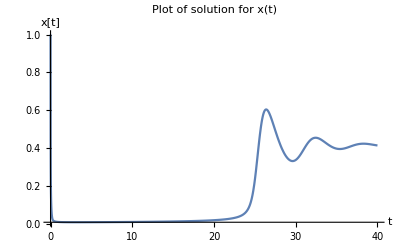

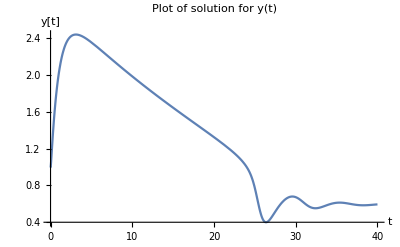

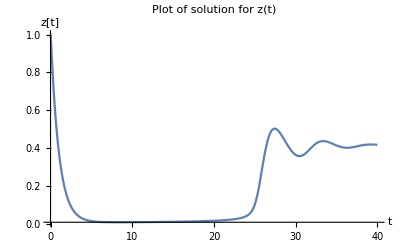

```mathematica
Plot[x[t]/.sol3b,{t,0,40},PlotRange->Full, AxesLabel->{"t","x[t]"},
PlotLabel-> "Plot of solution for x(t)"  ]
Plot[y[t]/.sol3b,{t,0,40},PlotRange->Full, AxesLabel->{"t","y[t]"},
PlotLabel-> "Plot of solution for y(t)"  ]
Plot[z[t]/.sol3b,{t,0,40},PlotRange->Full, AxesLabel->{"t","z[t]"},
PlotLabel-> "Plot of solution for z(t)"  ]
```

#### Part c:

(c) In part (b)  you should find that the results are tending towards constant values. Rewrite the original equations for the steady state case (time derivatives set to zero) and solve analytically for the steady state values of x,y and z  in terms of ϵ, q, δ and f. [4]

```mathematica
steadyst={deq3a,deq3b,deq3c}/.{x'[t]-> 0,y'[t]-> 0,z'[t]-> 0}//Simplify
sol3c =Solve[steadyst,{x[t],y[t],z[t]}]
```

{(x[t]^2+x[t] (-1+y[t])-q y[t])/ϵ==0,((q+x[t]) y[t]-2 f z[t])/δ==0,x[t]==z[t]}

{{x[t]→0,y[t]→0,z[t]→0},{x[t]→1/2 (1-2 f-q-√(1-4 f+4 f^2+2 q+12 f q+q^2)),y[t]→(q+6 f q+q^2+q √(1-4 f+4 f^2+2 q+12 f q+q^2))/(4 q),z[t]→1/2 (1-2 f-q-√(1-4 f+4 f^2+2 q+12 f q+q^2))},{x[t]→1/2 (1-2 f-q+√(1-4 f+4 f^2+2 q+12 f q+q^2)),y[t]→(q+6 f q+q^2-q √(1-4 f+4 f^2+2 q+12 f q+q^2))/(4 q),z[t]→1/2 (1-2 f-q+√(1-4 f+4 f^2+2 q+12 f q+q^2))}}

#### Part d:

(d) Substitute the values of the parameters from (b) into your answers from (c). [2]

```mathematica
sol3d = sol3c/.val3b
```

{{x[t]→0,y[t]→0,z[t]→0},{x[t]→-0.0193092,y[t]→0.809655,z[t]→-0.0193092},{x[t]→0.414309,y[t]→0.592845,z[t]→0.414309}}

#### Part e:

(e) Replot the results from (b), but on each  graph, include a straight line showing the appropriate steady state solution from (d) [3]

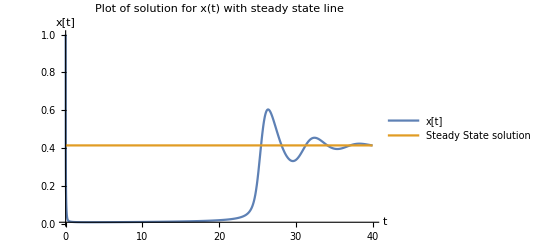

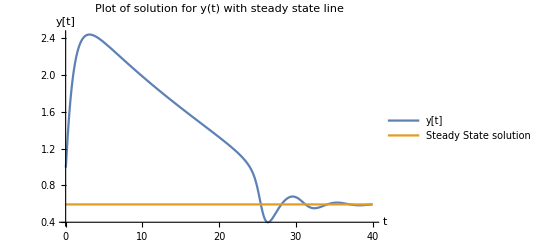

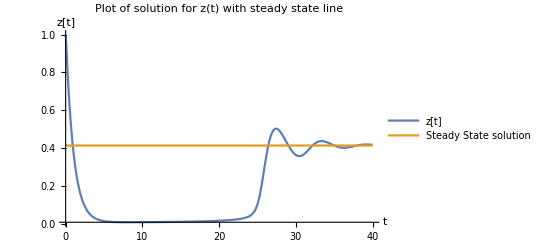

```mathematica
Plot[{x[t]/.sol3b,x[t]/.sol3d[[3]]},{t,0,40},PlotRange->Full, AxesLabel->{"t","x[t]"},
PlotLabel-> "Plot of solution for x(t) with steady state line", PlotLegends->{"x[t]","Steady State solution"}]

Plot[{y[t]/.sol3b,y[t]/.sol3d[[3]]},{t,0,40},PlotRange->Full, AxesLabel->{"t","y[t]"},
PlotLabel-> "Plot of solution for y(t) with steady state line",PlotLegends->{"y[t]","Steady State solution"} ]

Plot[{z[t]/.sol3b,z[t]/.sol3d[[3]]},{t,0,40},PlotRange->Full, AxesLabel->{"t","z[t]"},
PlotLabel-> "Plot of solution for z(t) with steady state line",PlotLegends->{"z[t]","Steady State solution"}]
```

Total marks available: 70

Solutions are due by 4pm on Monday March 16th.
Make a copy of your solutions with the output deleted (Cell|Delete All Output) and upload that file to Moodle.
Please name the file to include your family name and first name, for example I would use hw1_Jasvir_Bhamrah.

The first thing I shall do when I get the file is to click Evaluation|Evaluate Notebook, so make sure the file you send me will survive that.

A.H. Harker, J Underwood, 
UCL
February 2020